# VYA - Přednášky

## 5. Přednáška

### Obvody a uzlová napětí

Rovnice součástek

1) Najdi uzly a zvol referenční 
2) Označ proudy
3) ZZ Proudu : 0 = I_1 + I_2 + I_3 +...
4) Rovnice součástek

```mathematica
Quiet[Remove["Global`*"]];
```

```mathematica
R = 100;
μF = 10^-6;
mH = 0.001;
Cl = 4.7 μF;
L = 33mH;
Uz = 10*Tanh[5*Sin[314t]];
Iz = 0.01*Sin[√2 * 314t];
```

```mathematica
Rovn = {0 == IC[t] + IR[t] + IUz[t],
IUz[t] + Iz == IL[t],
U1[t] == R * IR[t],
IC[t] == Cl * U1'[t],
U2[t] == L * IL'[t],
Uz == U1[t] - U2[t] }
```

{0==IC[t]+IR[t]+IUz[t],IUz[t]+0.01 Sin[314 √2 t]==IL[t],U1[t]==100 IR[t],IC[t]==4.7×10^-6 U1'[t],U2[t]==0.033 IL'[t],10 Tanh[5 Sin[314 t]]==U1[t]-U2[t]}

### Cases

```mathematica
?Cases
```

```mathematica
Cases[Rovn, _[t], {0, ∞}]
```

{IC[t],IL[t],IUz[t],IUz[t],IL[t],U1[t],IR[t],IC[t],U1'[t],U2[t],IL'[t],U1[t],U2[t]}

```mathematica
?Union
```

```mathematica
Union[Cases[Rovn, _[t], {0, ∞}]]
```

{IC[t],IL[t],IR[t],IUz[t],U1[t],U2[t],IL'[t],U1'[t]}

```mathematica
FullForm[IL'[t]]
```

Derivative[1][IL][t]

```mathematica
Nezname = Union[Cases[Rovn, a_Symbol[t] :> a, {0, ∞}]]
```

{IC,IL,IR,IUz,U1,U2}

```mathematica
Length /@ {Rovn, Nezname}
PocPod = Union[Cases[Rovn, a_'[t] :> a[0] == 0, {0, ∞}]]
```

{6,6}

{IL[0]==0,U1[0]==0}

```mathematica
RovnPod = Union[Rovn, PocPod]
```

{0==IC[t]+IR[t]+IUz[t],IC[t]==4.7×10^-6 U1'[t],IL[0]==0,IUz[t]+0.01 Sin[314 √2 t]==IL[t],10 Tanh[5 Sin[314 t]]==U1[t]-U2[t],U1[0]==0,U1[t]==100 IR[t],U2[t]==0.033 IL'[t]}

```mathematica
tMax = 0.08;
Res = NDSolve[RovnPod, Nezname, {t, 0, tMax}, StartingStepSize->10^-9][[1]]
```

{IC→InterpolatingFunction[…],IL→InterpolatingFunction[…],IR→InterpolatingFunction[…],IUz→InterpolatingFunction[…],U1→InterpolatingFunction[…],U2→InterpolatingFunction[…]}

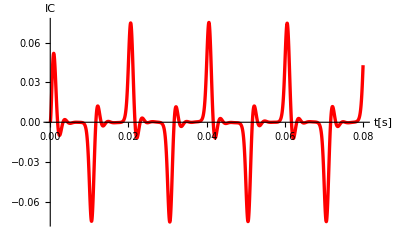
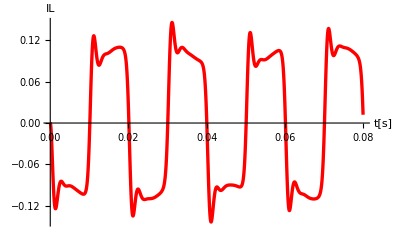
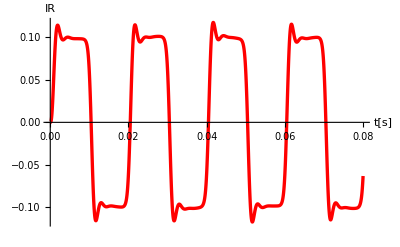
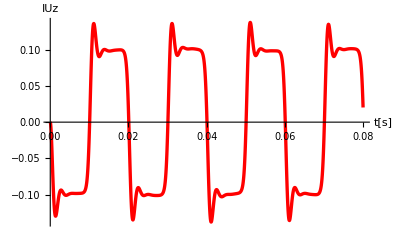
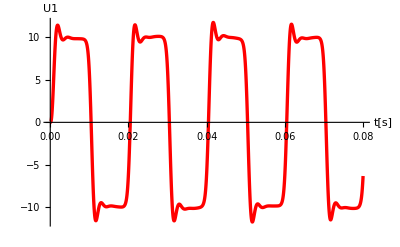
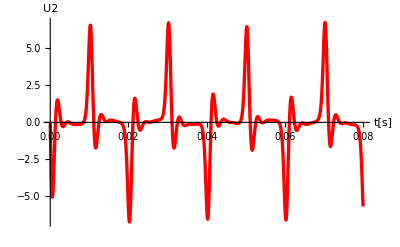

```mathematica
Plot[#[t] /. Res, {t, 0, tMax}, AxesLabel->{"t[s]", ToString[#]}, PlotRange->All, GridLines->Full, PlotStyle->{Red, Thickness[0.006]}] & /@ Nezname
```

```mathematica
Options[NDSolve]
```

{AccuracyGoal→Automatic,Compiled→Automatic,DependentVariables→Automatic,DiscreteVariables→{},EvaluationMonitor→None,InitialSeeding→{},InterpolationOrder→Automatic,MaxStepFraction→1/10,MaxSteps→Automatic,MaxStepSize→Automatic,Method→Automatic,NormFunction→Automatic,PrecisionGoal→Automatic,StartingStepSize→Automatic,StepMonitor→None,WorkingPrecision→MachinePrecision}